```mathematica
(*  Create a sequence (called 'ob' for observations) that          *)(*  has independent errors.                                        *)
```

```mathematica
f[x_, a_, b_, σ_]:= a + b * x + Random[NormalDistribution[0, σ]]
```

```mathematica
ob= Table[{0.1 * n, f[0.1 * n, 1, 1.5,1]}, {n, 1, 80}];
```

```mathematica
(*   Graph the sequence.                                           *)
```

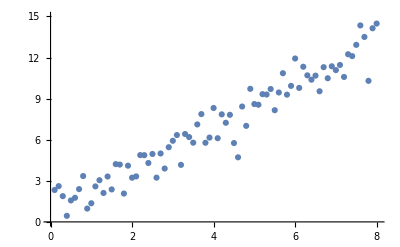

```mathematica
ListPlot[ob, AxesOrigin -> {0, 0}, PlotRange -> {{0, 8.02}, {Floor[Min[Transpose[ob][[2]]]], Ceiling[Max[Transpose[ob][[2]]]]}}]
```

```mathematica
(*  Estimate a linear model that fits the sequence and produce  *)
(*  a parameter table for the model.                            *)
```

```mathematica
r = LinearModelFit[ob,{x},x]
```

FittedModel[0.809416+1.53583 x]

```mathematica
r["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.809416 | 0.223384 | 3.62343 | 0.000515734
x | 1.53583 | 0.0479151 | 32.0532 | 1.15963×10^-46

```mathematica
(*  Form a sequence of predicted values from the estimated        *)(*  linear model.                                                 *)
```

```mathematica
(*  Before we can calculate the predicted values we need to pull  *)
(*  the slope and intercept out of the parameter table from the   *)
(*  regression.                                                   *)
```

```mathematica
r["ParameterTable"][[1, 1]]
```

{{,Estimate,Standard Error,t-Statistic,P-Value},{1,0.809416,0.223384,3.62343,0.000515734},{x,1.53583,0.0479151,32.0532,1.15963×10^-46}}

```mathematica
r["ParameterTable"][[1, 1, 2, 2]]
```

0.809416

```mathematica
r["ParameterTable"][[1, 1, 3, 2]]
```

1.53583

```mathematica
p = Table[{0.1 * n, r["ParameterTable"][[1, 1, 2, 2]] + r["ParameterTable"][[1, 1, 3, 2]] * (0.1 * n)}, {n, 1, 80}];
```

```mathematica
(*  Form the errors (called 'e') from the difference between    *)
(*  the observed and predicted values.                          *)
```

```mathematica
e = Transpose[ob][[2]] - Transpose[p][[2]];
```

```mathematica
(*  Graph the errors.                                            *)
```

```mathematica
xyResiduals = Transpose[{Transpose[ob][[1]], e}];
```

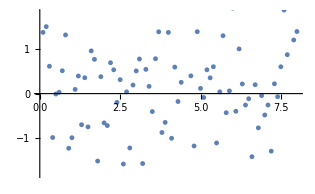

```mathematica
ListPlot[xyResiduals, AxesOrigin -> {0, 0}, LabelStyle->Directive[Medium], PlotRange -> {{0, 8.01}, {-1.8, 1.8}}]
```

```mathematica
(*  Calculate the change in the error terms.                    *)
```

```mathematica
de = Drop[e, 1] - Drop[e, -1];
```

```mathematica
(*  Calculate the Durbin-Watson statistic 'd'.                  *)
```

```mathematica
d = Sum[ de[[i]]^2, {i, 1, Length[de]}]/Sum[e[[i]]^2, {i, 1, Length[e]}]
```

2.08683

```mathematica
(*  The preceeding steps were used to find the Durbin-Watson         *)
(*  statistic for one sample sequence from a distribution with       *)
(*  independent, identically distributed errors and no serial        *)
(*  correlation.  The next function can be used to simulate          *)
(*  thousands of these test statistics in order to produce a         *)
(*  critical value for the test statistic.  The variable N in        *)
(*  function is the length of the sample.                            *)
```

```mathematica
DurbinWatson[N_, a_, b_, σ_]:= Module[{ob, r,D, y0, y1, p, e, de, e2, de2, r2, s},
ob = Table[f[n, a, b, σ], {n, 1, N}];
r = LinearModelFit[ob,{y},y];
D = r["DurbinWatsonD"];
y0 = r["ParameterTable"][[1, 1, 2, 2]];
y1 = r["ParameterTable"][[1, 1, 3, 2]];
p = Table[y0 + y1 *  n, {n, 1, N}];
e = ob - p;
de = Drop[e, 1] - Drop[e, -1];
e2 = Sum[e[[i]]^2, {i, 1, Length[e]}];
de2 = Sum[de[[i]]^2, {i, 1, Length[de]}];
de2/e2]
```

```mathematica
DurbinWatson[80, 1, 1.5, 1]
```

2.46287

```mathematica
(*  Run 1 million simulations of the model with no serial         *)(*  correlation with series length 80 in each simulation.         *)
```

```mathematica
dStats80= ParallelTable[DurbinWatson[80, 1, 1.5, 1], {i, 1,1000000}];
```

```mathematica
dStats80sort = Sort[dStats80];
```

```mathematica
(*  The mean of this distribution for 1 million simulations is    *)(*  2.02574.                                                      *)
```

```mathematica
{Mean[dStats80sort], Median[dStats80sort]}
```

{2.02573,2.0298}

```mathematica
(*  Only 5% of the Durbin-Watson statistics are smaller than      *)(*  element 50000 from the sorted array of 1 million              *)
(*  Durbin-Watson statistics.                                     *)
```

```mathematica
{dStats80sort[[50000]], dStats80sort[[10000]], dStats80sort[[1000]],dStats80sort[[100]],dStats80sort[[10]],dStats80sort[[1]]}
```

{1.65387,1.49733,1.31703,1.16799,1.02779,0.921924}

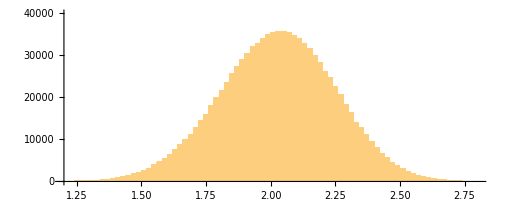

```mathematica
Histogram[dStats80, {0.02}, PlotRange -> {{1.2, 2.8}, {0, 40000}}, AxesOrigin -> {1.2, 0}, AspectRatio -> 0.4]
```

```mathematica
(*  THIS IS THE FIRST HOMEWORK PROBLEM.                           *)
(*  The critical value for a 5% test for serial correlation       *)
(*  depends on the sequence length.  In the previous calculation  *)
(*  we found that when the sequence length is 80 the critical     *)
(*  value for a 5% test is 1.654.  Repeat that calculation with   *)
(*  sequence lengths of 200.  Start by finding a distribution     *)
(*  of Durbin-Watson statistics using this function:              *)(*  ParallelTable[DurbinWatson[200, 1, 1.5, 1], {i, 1, 10000}];  *)
(*  Use the output of that function to find the critical value    *)
(*  for a 5% test for serial correlation.                         *)
```

```mathematica
(*  THIS IS THE END OF THE SECTION ON DURBIN-WATSON STATISTICS    *)
(*  IN A MODEL WITHOUT SERIAL CORRELATION.                        *)
```

```mathematica
(*  The derivation above can be modified to calculate the       *)
(*  Durbin-Watson statistic for an autoregressive price         *)
(*  sequence.                                                   *)
```

```mathematica
(*  The function NormalRVs[n] generates a sequence of 'n'       *)
(*  independent normal random variables with mean zero          *)(*  and variance 2.  The variance can be changed directly       *)
(*  in the function definition.                                 *)
```

```mathematica
NormalRVs[n_, σ_]:= Table[Random[NormalDistribution[0, σ]], {i, 1, n}]
```

```mathematica
(*  The function PriceSequence[] generates an autoregressive   *)
(*  sequence of length 'n' with adjustment rate 'c', initial   *)
(*  price p0, equilibrium price pStar.                         *)

PriceSequence[c_, p0_, pStar_, n_, σ_]:= 
       Module[{rv, p, start},
              rv = NormalRVs[n, σ];
              p = {p0};
              Label[start];
              p = Join[p, {p[[-1]] + c * (pStar - p[[-1]]) + 
                           rv[[Length[p]]]}];
              If[Length[p] < n, Goto[start]];
              Return[p]]
```

```mathematica
PriceSequenceGraph[c_, p0_, pStar_, n_, σ_]:= 
        Module[{s, r, x, p, i, range, o}, 
            Off[General::munfl];
                s = PriceSequence[c, p0, pStar, n, σ]; 
                r = LinearModelFit[s,{x},x];
           range = {{0, n}, {10 * Floor[0.1 * Min[s]], 
                                  10 * Ceiling[0.1 * Max[s]]}};
                Show[ListPlot[s, Joined -> True, PlotRange -> range, 
                              AxesOrigin -> {0, 10 * Floor[0.1 * Min[s]]}, AspectRatio -> 0.5], 
                      ListPlot[s],
                     Graphics[{Dashing[{0.01, 0.01, 0.01}], 
                               Line[{{0, r["ParameterTable"][[1, 1, 2, 2]]}, {n, r["ParameterTable"][[1, 1, 2, 2]]+ r["ParameterTable"][[1, 1, 3, 2]] * n}}]}]]]
```

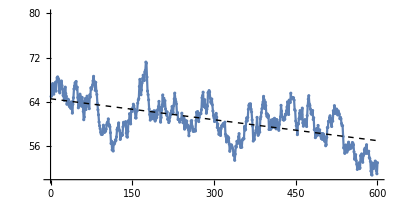

```mathematica
PriceSequenceGraph[0.02, 65, 60, 600, 1]
```

```mathematica
ob = PriceSequence[0.02, 65, 60, 80, 1];
```

```mathematica
r = LinearModelFit[ob,{y},y]
```

FittedModel[64.1094-0.0898731 y]

```mathematica
p = Table[r["ParameterTable"][[1, 1, 2, 2]] + r["ParameterTable"][[1, 1, 3, 2]] * n, {n, 1, 80}];
```

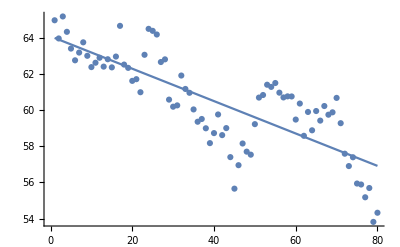

```mathematica
Show[ListPlot[ob], ListPlot[p, Joined -> True]]
```

```mathematica
e = ob - p;
```

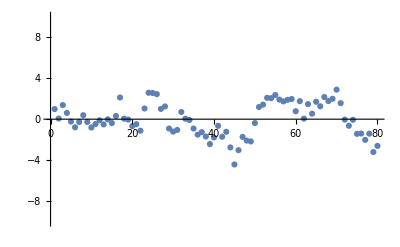

```mathematica
ListPlot[e, AxesOrigin -> {0, 0}, PlotRange -> {{0, 80}, {-10,10}}]
```

```mathematica
de = Drop[e, 1] - Drop[e, -1];
```

```mathematica
d = Sum[de[[i]]^2, {i, 1, Length[de]}]/Sum[e[[i]]^2, {i, 1, Length[e]}]
```

0.376571

```mathematica
DurbinWatsonAR[N_, c_, p0_, pStar_, σ_]:= Module[{ob, r, y0, y1, p, e, de, e2, de2, r2, s},
ob = PriceSequence[c, p0, pStar, N, σ];
r = LinearModelFit[ob,{y},y];
y0 = r["ParameterTable"][[1, 1, 2, 2]];
y1 = r["ParameterTable"][[1, 1, 3, 2]];
p = Table[y0 + y1 * n, {n, 1, N}];
e = ob - p;
e2 = Sum[e[[i]]^2, {i, 1, Length[e]}];
de = Drop[e, 1] - Drop[e, -1];
de2 = Sum[de[[i]]^2, {i, 1, Length[de]}];
de2/e2]
```

```mathematica
DurbinWatsonAR[80, 0.02, 50, 60, 1]
```

0.492601

```mathematica
dStatsAR80 = ParallelTable[DurbinWatsonAR[100, 0, 0, 0, 1], {i, 1, 100000}];
```

```mathematica
dStatsAR80sort = Sort[dStatsAR80];
```

```mathematica
{Mean[dStatsAR80sort], Median[dStatsAR80sort]}
```

{0.199564,0.177725}

```mathematica
{dStatsAR80sort[[95000]], dStatsAR80sort[[99000]], dStatsAR80sort[[99900]], dStatsAR80sort[[100000]]}
```

{0.406946,0.53701,0.70845,1.03712}

```mathematica
dStatsAR80 = ParallelTable[DurbinWatsonAR[100, 0.02, 50, 60, 1], {i, 1, 100000}];
```

```mathematica
dStatsAR80sort = Sort[dStatsAR80];
```

```mathematica
{dStatsAR80sort[[95000]], dStatsAR80sort[[99000]], dStatsAR80sort[[99900]], dStatsAR80sort[[100000]]}
```

{0.419082,0.551396,0.723482,1.05544}

```mathematica
dStatsAR80 = ParallelTable[DurbinWatsonAR[100, 0.2, 50, 60, 1], {i, 1, 100000}];
```

```mathematica
dStatsAR80sort = Sort[dStatsAR80];
```

```mathematica
{dStatsAR80sort[[95000]], dStatsAR80sort[[99000]], dStatsAR80sort[[99900]], dStatsAR80sort[[100000]]}
```

{0.448918,0.527569,0.625283,0.850851}

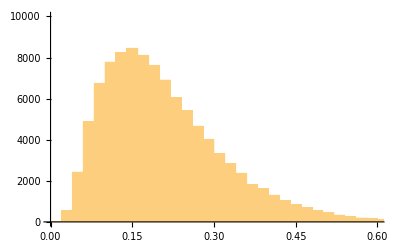

```mathematica
Histogram[dStatsAR80, {0.02},PlotRange -> {{0, 0.6}, {0, 10000}}, AxesOrigin -> {0.0, 0}]
```

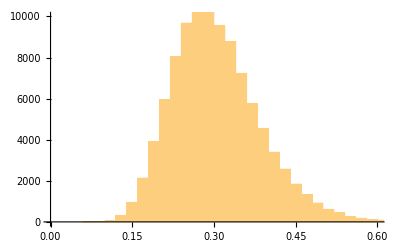

```mathematica
Histogram[dStatsAR80, {0.02},PlotRange -> {{0, 0.6}, {0, 10000}}, AxesOrigin -> {0.0, 0}]
```

```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Data\BRLpCADpGBPpJPYpMXNpNOKpTRLpUSD.txt;
```

```mathematica
(*  The function Durbin-Watson can be modified to take a vector   *)
(*  of data rather than simulate data.  With this modification    *)
(*  to the function we can calculate Durbin-Watson statistics     *) 
(*  series like the US dollar to British pound exchange rate.     *)
```

```mathematica
DurbinWatson[data_]:= Module[{N, r, y0, y1, p, e, de, r2, s},
N = Length[data];
r = LinearModelFit[data,{y},y];
y0 = r["ParameterTable"][[1, 1, 2, 2]];
y1 = r["ParameterTable"][[1, 1, 3, 2]];
p = Table[y0 + y1 *  n, {n, 1, N}];
e = data - p;
de = Drop[e, 1] - Drop[e, -1];
Sum[de[[i]]^2, {i, 1, Length[de]}]/Sum[e[[i]]^2, {i, 1, Length[e]}]]
```

```mathematica
Mean[USDpGBP][[2]]
```

1.45652

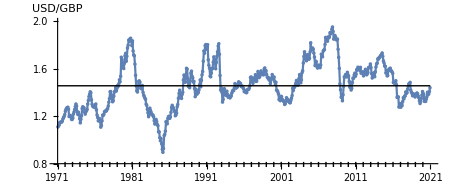

```mathematica
Show[ListPlot[USDpGBP, AxesOrigin -> {1971, 0.8}, PlotRange -> {{1971, 2021}, {0.8, 2.0}}, AxesLabel -> {"", "USD/GBP"},Ticks -> {Table[1971 + 5 * i, {i, 0, 10}], Automatic}, AspectRatio -> 0.4],ListPlot[USDpGBP, AxesOrigin -> {1971, 0}, PlotRange -> {{1971,2021}, {0.8, 2.0}}, Joined -> True], Graphics[Line[{{1971, Mean[USDpGBP][[2]]}, {2021, Mean[USDpGBP][[2]]}}]],
Graphics[Table[Line[{{1971 + i, 0}, {1971 + i, 0.815}}], {i, 1, 49}]]]
```

```mathematica
DurbinWatson[Transpose[USDpGBP][[2]]]
```

0.0403236

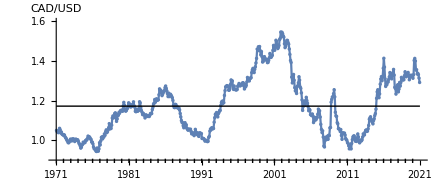

```mathematica
Show[ListPlot[CADpUSD, AxesOrigin -> {1971, 0.9}, PlotRange -> {{1971, 2021}, {0.9, 1.6}}, AxesLabel -> {"", "CAD/USD"},Ticks -> {Table[1971 + 5 * i, {i, 0, 10}], Automatic}, AspectRatio -> 0.4],ListPlot[CADpUSD, AxesOrigin -> {1971, 0}, PlotRange -> {{1971,2021}, {0.9, 1.6}}, Joined -> True], Graphics[Line[{{1971, Mean[CADpUSD][[2]]}, {2021, Mean[CADpUSD][[2]]}}]],
Graphics[Table[Line[{{1971 + i, 0}, {1971 + i, 0.907}}], {i, 1, 49}]]]
```

```mathematica
DurbinWatson[Transpose[CADpUSD][[2]]]
```

0.0174188